# w = w_0+w_a*z/(1+z)

```mathematica
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb];
```

## Constants

```mathematica
ompl=0.315; (*times apo x^2 *)
hcpl = 0.674;
H0pl=100*hcpl;
w0cpl =-1.07;
wacpl  = 0.24;
Gc = 6.674*10^(-11);
k1=3*H0pl^2/(8*Pi*Gc);
```

## W (z)

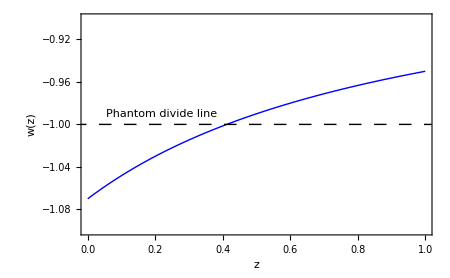

```mathematica
wz[z_,w0_?NumberQ,wa_?NumberQ] := w0+wa*(z/(1+z));
pltcpl01 = Plot[wz[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,Frame->True,FrameLabel->{"z","w(z)"},PlotStyle->{Blue,Thick},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{0,1},{-1.1,-0.9}},Epilog->{{Dashing[0.02],Line[{{-30,-1},{8,-1}}]},Text["Phantom divide line",{0.22,-0.99}]}]
```

## ρ_DE (z)

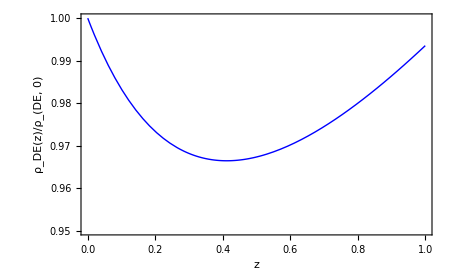

```mathematica
rde[z_,w0_,wa_]:= (1+z)^(3*(1+w0+wa))*Exp[-3*wa*z/(1+z)]
rde[z_,w0_,wa_];
Plot[rde[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,BaseStyle->{FontFamily->"Times",18},Frame->True,FrameLabel->{"z","ρ_DE(z)/ρ_(DE, 0)"},PlotStyle->{Blue,Thick},PlotRange->{{0,1},{0.95,1}},Epilog->{{Dashing[0.02],Line[{{-30,-1},{8,-1}}]},Text["Phantom divide line",{0.22,-0.99}]}]
```

## V (z)

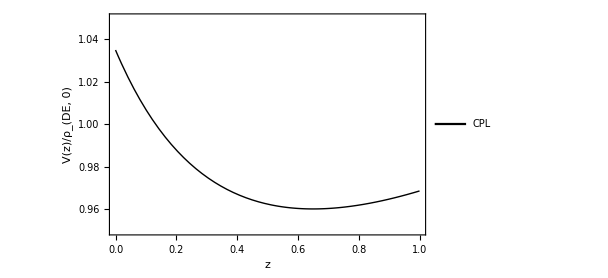

```mathematica
vz[z_,w0_,wa_]:=1/2*(1-w0-wa*z/(1+z))*(1+z)^(3*(1+w0+wa))*Exp[-3*wa*z/(1+z)]
vz[z_,w0_,wa_];
plv1 =Plot[vz[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z","V(z)/ρ_(DE, 0)"},PlotStyle->{Black,Thick},PlotRange->{{0,1},{0.95,1.05}},PlotLegends->Placed[{"CPL"},{Right,Top}]]
```

## H (z)

```mathematica
hzz[z_,w0_,wa_]:=H0pl*Sqrt[(ompl*(1+z)^3+(1-ompl)*(1+z)^(3*(1+w0+wa))*Exp[-3*wa*z/(1+z)])]
```

```mathematica
hzz[z,w0,wa];
```

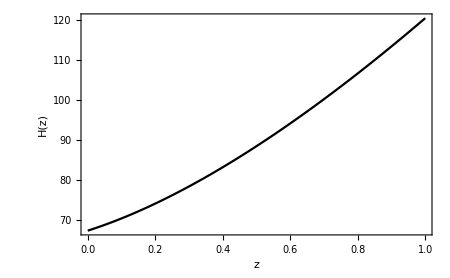

```mathematica
plcpl = Plot[hzz[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z","H(z)"},PlotStyle->{Black}]
```

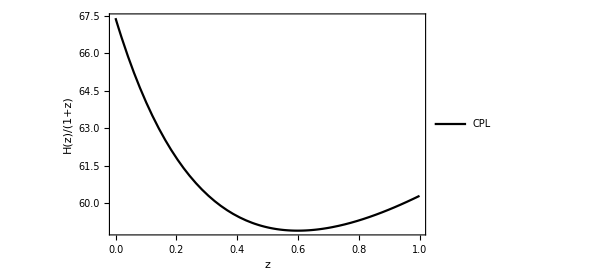

```mathematica
plcpl1 = Plot[hzz[z,w0cpl,wacpl]/(1+z),{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z","H(z)/(1+z)"},PlotStyle->{Black},PlotLegends->Placed[{"CPL"},{Right,Top}]]
```

## φ (z)

```mathematica
f1z[z_,w0_?NumberQ,wa_?NumberQ]:= Sqrt[Abs[1+w0+wa*z/(1+z)]]/((1+z)*Sqrt[1-ompl+ompl*(1+z)^(-3*(w0+wa))*Exp[3*wa*z/(1+z)]])
fzz[z_]:= NIntegrate[f1z[Z,w0cpl,wacpl],{Z,0,z}]
```

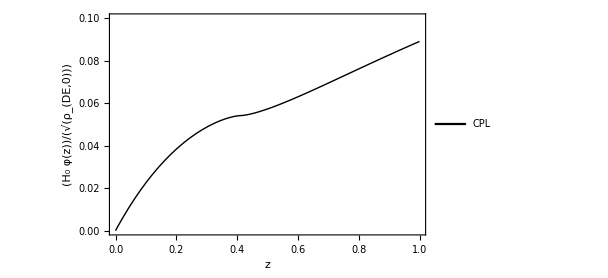

```mathematica
plf1 = Plot[fzz[z],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",φ[z]*(Subscript[H, 0]/(Sqrt[Subscript[ρ, DE,0]]))},PlotStyle->{Black,Thick},PlotRange->{{0,1},{0,0.1}},PlotLegends->Placed[{"CPL"},{Right,Top}]]
```

### φ2

```mathematica
phisq[z_,w0_?NumberQ,wa_?NumberQ] := 1+w0+wa*z/(1+z)*rde[z,w0,wa]
```

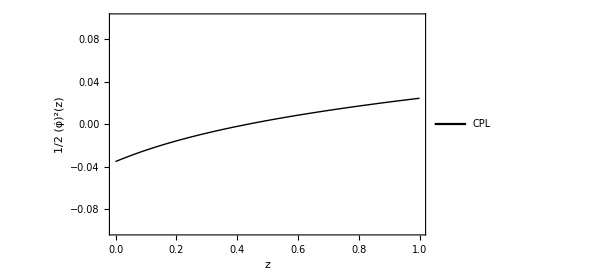

```mathematica
plfd1 = Plot[0.5*phisq[z,w0cpl,wacpl],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",(OverDot[φ]^2)[z]/2},PlotStyle->{Black,Thick},PlotRange->{{0,1},{-0.1,0.1}},PlotLegends->Placed[{"CPL"},{Right,Bottom}]]
```

## V (φ)

```mathematica
(*ParametricPlot[{fzz[z],vz[z,-0.5,-0.3]},{z,0,1},PlotRange->Automatic]*)
points1=ParallelTable[{fzz[z],vz[z,w0cpl,wacpl]},{z,Range[0,1,0.001]}];//AbsoluteTiming
pl1=ListPlot[points1,PlotLegends->Placed[{"CPL"},{Right,Top}]];
```

{52.1055,Null}

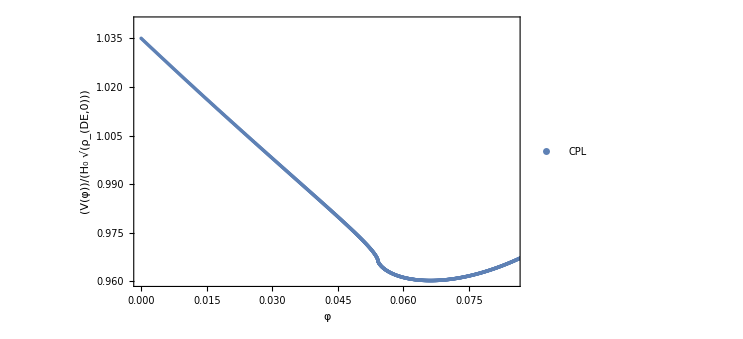

```mathematica
Show[pl1,ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"φ",V[φ]/(Subscript[H, 0]*Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Black,Thick},PlotRange->{{0,0.085},{0.96,1.04}}]
```

## ΛCDM

```mathematica
ompl
H0pl
```

0.315

67.4

```mathematica
ompl=0.317; (*times apo x^2 *)
hlcdm = "0.672";
H0pl=100*hlcdm;
ompl
```

0.317

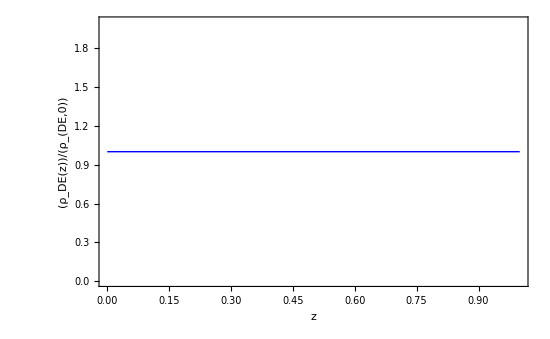

```mathematica
Plot[rde[z,-1,0],{z,0,1},ImageSize ->550,PlotRange->{{0,1},Automatic},BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",Subscript[ρ, DE][z]/Subscript[ρ, DE,0]},PlotStyle->{Blue,Thick}]
```

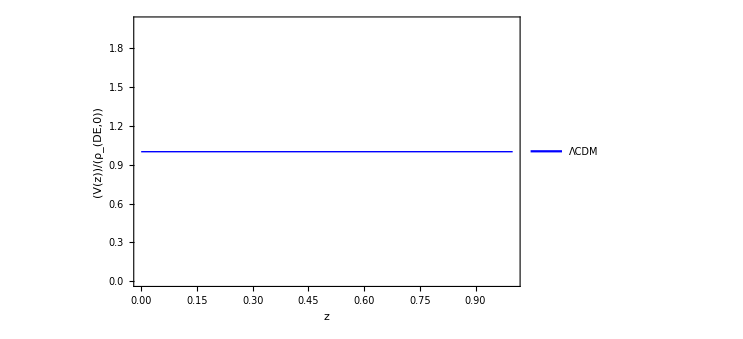

```mathematica
plv3 = Plot[vz[z,-1,0],{z,0,1},ImageSize ->550,PlotRange->{{0,1},Automatic},BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",V[z]/Subscript[ρ, DE,0]},PlotStyle->{Blue,Thick},PlotLegends->Placed[{"ΛCDM"},{Right,Top}]]
```

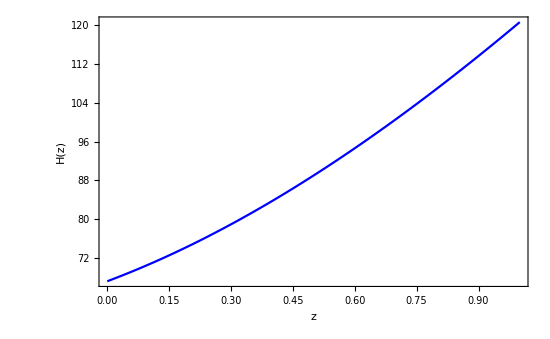

```mathematica
pll = Plot[hzz[z,-1,0],{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",H[z]},PlotStyle->{Blue}]
```

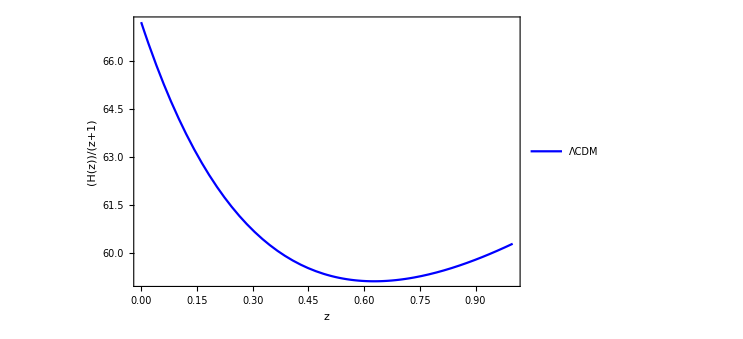

```mathematica
pll1 = Plot[hzz[z,-1,0]/(1+z),{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",H[z]/(1+z)},PlotStyle->{Blue},PlotLegends->Placed[{"ΛCDM"},{Right,Top}]]
```

```mathematica
hzz[1,-1,0]//N
```

120.603

```mathematica
f1z[z,-1,0]
```

0

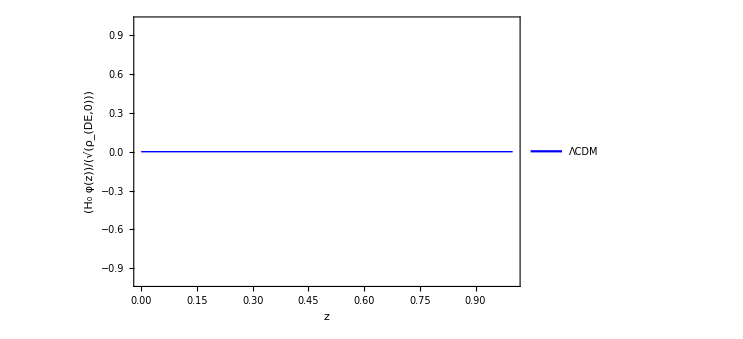

```mathematica
plf3 = Plot[f1z[z,-1,0],{z,0,1},PlotRange->{{0,1},Automatic},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",(φ[z]*Subscript[H, 0])/(Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Blue,Thick},PlotLegends->Placed[{"ΛCDM"},{Right,Top}]]
```

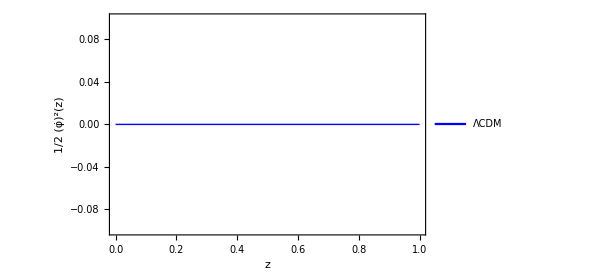

```mathematica
plfd3 = Plot[0.5*phisq[z,-1,0],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",(OverDot[φ]^2)[z]/2},PlotStyle->{Blue,Thick},PlotRange->{{0,1},{-0.1,0.1}},PlotLegends->Placed[{"ΛCDM"},{Right,Bottom}]]
```

```mathematica
Clear[ompl,H0pl]
```

## wCDM

```mathematica
ompl=0.315; (*times apo x^2 *)
hwcdm = 0.675;
H0pl=100*hwcdm;
w0wcdm = "-1.01";
```

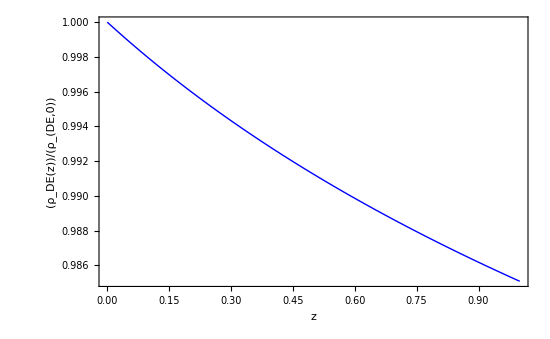

```mathematica
Plot[rde[z,w0wcdm,0],{z,0,1},PlotRange->{{0,1},Automatic},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",Subscript[ρ, DE][z]/Subscript[ρ, DE,0]},PlotStyle->{Blue,Thick}]
```

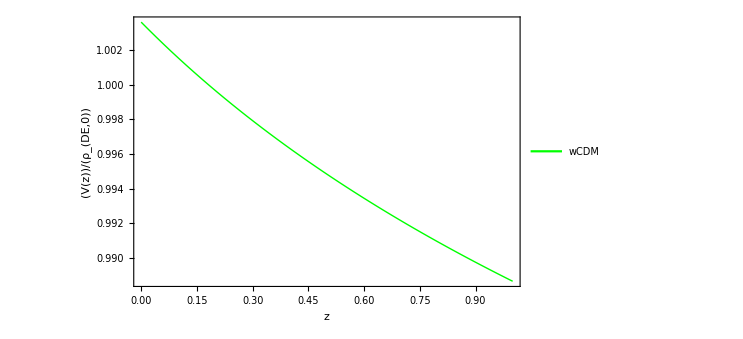

```mathematica
plv2 = Plot[vz[z,w0wcdm,0],{z,0,1},ImageSize ->550,PlotRange->{{0,1},Automatic},BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",V[z]/Subscript[ρ, DE,0]},PlotStyle->{Green,Thick},PlotLegends->Placed[{"wCDM"},{Right,Top}]]
```

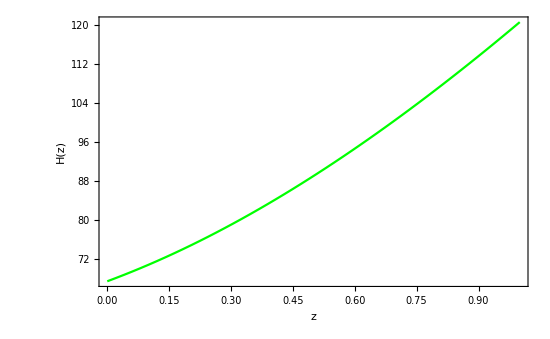

```mathematica
plw = Plot[hzz[z,w0wcdm,0],{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",H[z]},PlotStyle->{Green}]
```

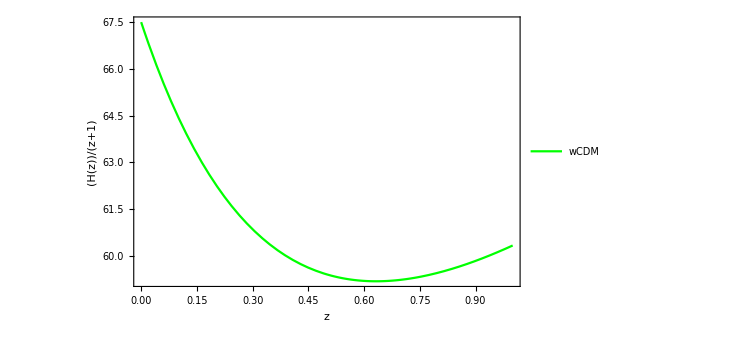

```mathematica
plw1 = Plot[hzz[z,w0wcdm,0]/(1+z),{z,0,1},ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",H[z]/(1+z)},PlotStyle->{Green},PlotLegends->Placed[{"wCDM"},{Right,Top}]]
```

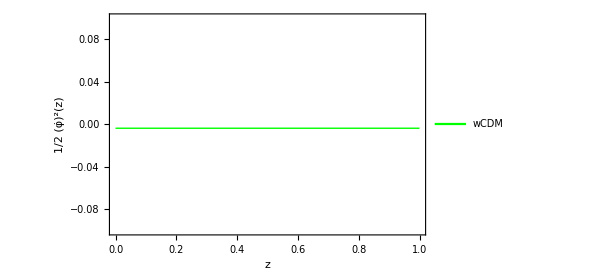

```mathematica
plfd2 = Plot[0.5*phisq[z,w0wcdm,0],{z,0,1},ImageSize -> 450,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",(OverDot[φ]^2)[z]/2},PlotStyle->{Green,Thick},PlotRange->{{0,1},{-0.1,0.1}},PlotLegends->Placed[{"wCDM"},{Right,Bottom}]]
```

```mathematica
f2z[z_,w0_?NumberQ,wa_?NumberQ]:= Sqrt[Abs[1+w0+wa*z/(1+z)]]/((1+z)*Sqrt[1+ompl/(1-ompl)*(1+z)^(-3*(w0+wa))*Exp[3*wa*z/(1+z)]])
f2z[Z,w0wcdm,0]
fzzz[z_]:= NIntegrate[f2z[Z,w0wcdm,0],{Z,0,z}]
```

0.0849883/((1+Z) √(1+0.459854 (1+Z)^3.02167))

```mathematica
fzzz[1]
```

0.0384677

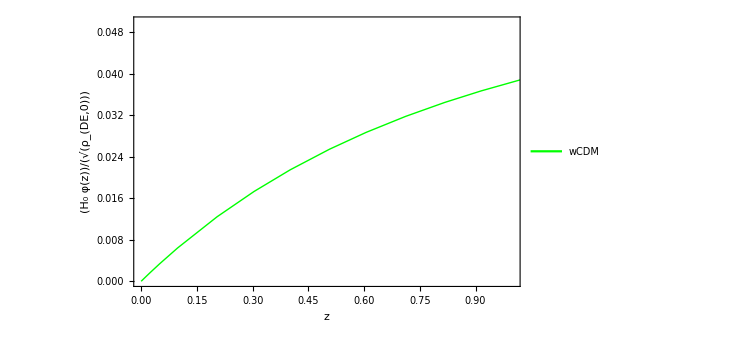

```mathematica
plf2 = Plot[fzzz[z],{z,0,5},ImageSize ->550,PlotRange->{{0,1},{0,0.05}},BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"z",(φ[z]*Subscript[H, 0])/(Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Green,Thick},PlotLegends->Placed[{"wCDM"},{Right,Top}]]
```

```mathematica
NIntegrate[f2z[Z,w0wcdm,0],{Z,0,1}]
```

0.0384677

```mathematica
k123z[z_]:=Integrate[f2z[Z,w0wcdm,0],Z]
k123z[z]
```

-0.0562526 ArcTanh[1. √(1.+0.459854 (1.+Z)^3.02167)]

```mathematica
Plot[k123z[z],{z,-5,5}];
```

```mathematica
Plot[-0.056ArcTanh[1.0004*Sqrt[1+0.46*(1+z)^3]],{z,-5,6}];
```

```mathematica
l1234[Z_] :=  1. √(1.+0.46141997410363805 (1.+Z)^3.0216900000000004)
p1[z_] :=1/2*Log[(1+l123[z])/(1-l123[z])]
```

```mathematica
lnpl[Z_] := 1/2 Log[(1+1. √(1.+0.46141997410363805 (1.+Z)^3.0216900000000004))/(1-1. √(1.+0.46141997410363805 (1.+Z)^3.0216900000000004))]
Plot[Re[lnpl[z]],{z,-1,10}];
```

```mathematica
Plot[l1234[z],{z,-1,10}];
```

```mathematica
l1234[0.001]
```

1.20947

```mathematica
lnpl[1]
```

0.495997+1.5708 ⅈ

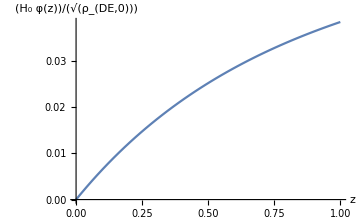

```mathematica
Plot[Re[fzzz[z]],{z,0,1},AxesLabel->{z,(φ[z]*Subscript[H, 0])/(Sqrt[Subscript[ρ, DE,0]])},LabelStyle->Directive[Black],ImageSize -> Medium,PlotRange->{{0,1},Automatic}]
```

## V (φ)

```mathematica
points2=ParallelTable[{fzzz[z],vz[z,w0wcdm,0]},{z,Range[0,1,0.01]}];
```

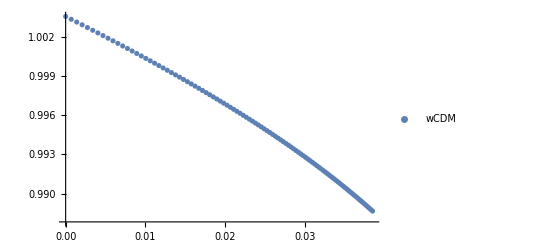

```mathematica
pl2=ListPlot[points2,PlotLegends->Placed[{"wCDM"},{Right,Top}]]
```

```mathematica
fzzz[1]//N
```

0.0384677

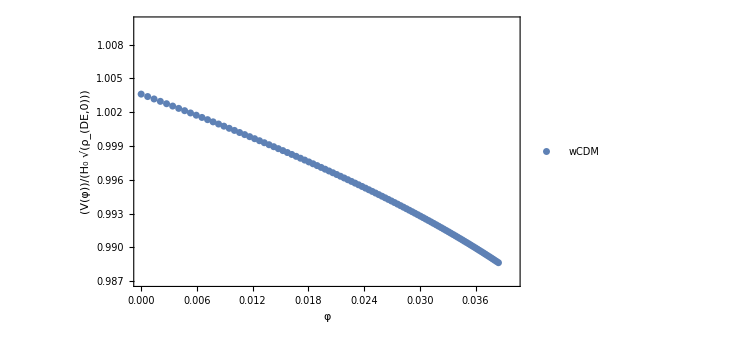

```mathematica
Show[pl2,ImageSize ->550,BaseStyle->{Large,FontFamily->"Times",18},Frame->True,FrameLabel->{"φ",V[φ]/(Subscript[H, 0]*Sqrt[Subscript[ρ, DE,0]])},PlotStyle->{Blue,Thick},PlotRange->{{0,0.04},{0.987,1.01}}]
```

```mathematica
Clear[ompl,H0pl,w0]
```

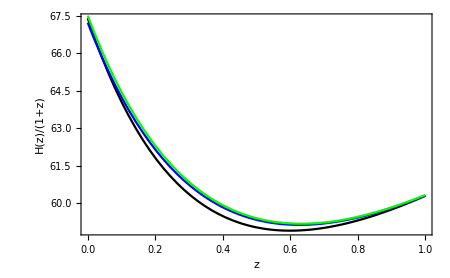

```mathematica
Show[plcpl1,pll1,plw1]
```

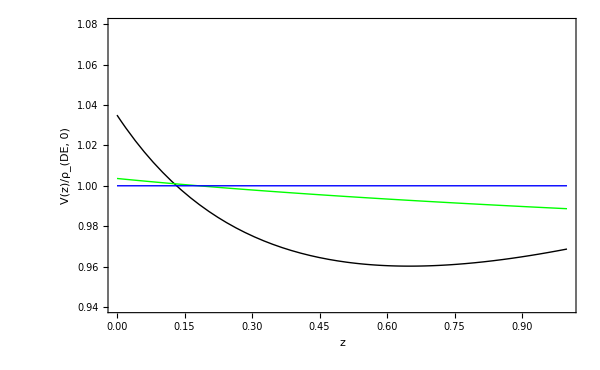

```mathematica
Show[plv1,plv2,plv3,PlotRange->{{0,1},{0.94,1.08}},ImageSize->600]
```

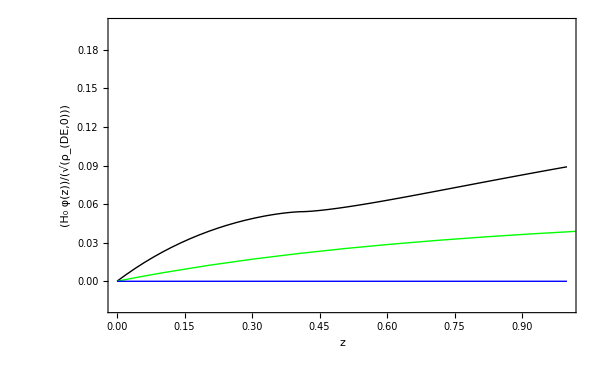

```mathematica
Show[plf1,plf2,plf3,PlotRange->{{0,1},{-0.02,0.2}},ImageSize->600]
```

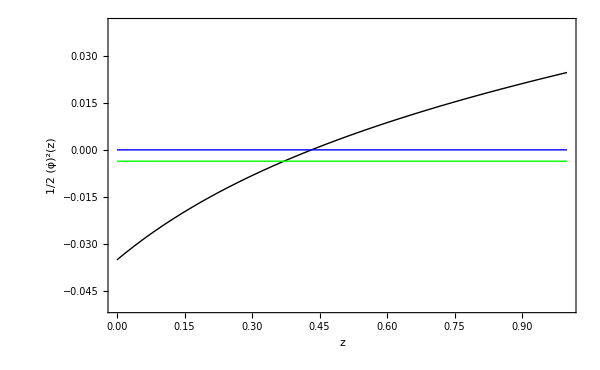

```mathematica
Show[plfd1,plfd2,plfd3,PlotRange->{{0,1},{-0.05,0.04}},ImageSize->600]
```

```mathematica
fzzz[50]
```

NIntegrate[f2z[Z,w0wcdm,0],{Z,0,50}]

```mathematica
f2z[z,-1.00723,0]
```

0.0850294/((1+z) √(1+(ompl (1+z)^3.02169)/(1-ompl)))

```mathematica
0.08502940667792566/((1+z) √(1+0.46141997410363805 (1+z)^3.0216900000000004))
Plot[f2z[z],{z,0,1}]
```

0.0850294/((1+z) √(1+0.46142 (1+z)^3.02169))

-Graphics-

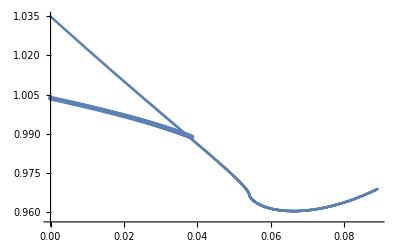

```mathematica
Show[pl1,pl2]
```